# Методи на Рунге-Кута за решаване задача на Коши с начално условие

## Задача 3 a) от файла

y’ = y/x+1, x ∈ [1,2]
y(1) = 0

търсим точно частно решение:

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x]/x+1, y[1] == 0}, y[x],x]
```

{{y[x]→x Log[x]}}

### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. f_i = 1. k1 = 0.25 k2 = 0.3 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.275 f_i = 1.22 k1 = 0.305 k2 = 0.346667 y_точно = 0.278929 истинска грешка = 0.00392944

i = 2 x_i = 1.5 y_i = 0.600833 f_i = 1.40056 k1 = 0.350139 k2 = 0.385853 y_точно = 0.608198 истинска грешка = 0.00736433

i = 3 x_i = 1.75 y_i = 0.968829 f_i = 1.55362 k1 = 0.388404 k2 = 0.419654 y_точно = 0.979328 истинска грешка = 0.0104983

i = 4 x_i = 2. y_i = 1.37286 f_i = 1.68643 k1 = 0.421607 k2 = 0.449385 y_точно = 1.38629 истинска грешка = 0.0134358

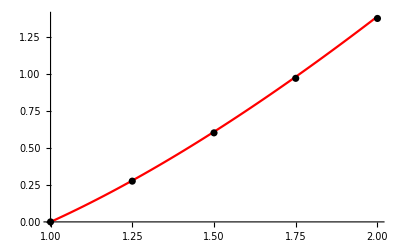

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h,y+k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (1/2,1/2) - модифициран метод на Ойлер

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. f_i = 1. k1 = 0.25 k2 = 0.277778 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.277778 f_i = 1.22222 k1 = 0.305556 k2 = 0.328283 y_точно = 0.278929 истинска грешка = 0.00115166

i = 2 x_i = 1.5 y_i = 0.606061 f_i = 1.40404 k1 = 0.35101 k2 = 0.370241 y_точно = 0.608198 истинска грешка = 0.00213706

i = 3 x_i = 1.75 y_i = 0.976301 f_i = 1.55789 k1 = 0.389472 k2 = 0.406138 y_точно = 0.979328 истинска грешка = 0.00302615

i = 4 x_i = 2. y_i = 1.38244 f_i = 1.69122 k1 = 0.422805 k2 = 0.437511 y_точно = 1.38629 истинска грешка = 0.00385458

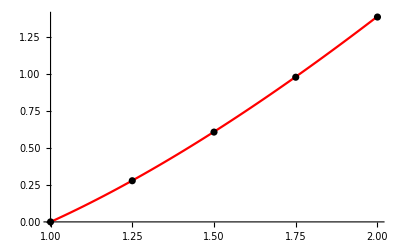

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h/2,y+k1/2];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 1. y_i = 0. f_i = 1. k1 = 0.25 k2 = 0.285714 y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.276786 f_i = 1.22143 k1 = 0.305357 k2 = 0.334769 y_точно = 0.278929 истинска грешка = 0.00214372

i = 2 x_i = 1.5 y_i = 0.604202 f_i = 1.4028 k1 = 0.3507 k2 = 0.3757 y_точно = 0.608198 истинска грешка = 0.00399598

i = 3 x_i = 1.75 y_i = 0.973652 f_i = 1.55637 k1 = 0.389093 k2 = 0.410832 y_точно = 0.979328 истинска грешка = 0.00567567

i = 4 x_i = 2. y_i = 1.37905 f_i = 1.68952 k1 = 0.422381 k2 = 0.441612 y_точно = 1.38629 истинска грешка = 0.00724492

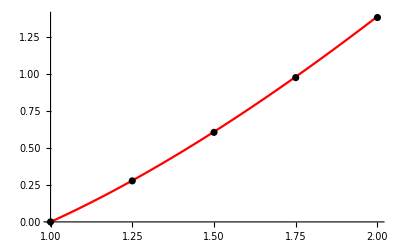

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+2/3*h,y+2/3*k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+ 1/4 k1 + 3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 1. y_i = 0. f_i = 1. k1 = 0.25 k2 = 0.277778 k3= 0.280864 k4= 0.306173y_точно = 0. истинска грешка = 0.

i = 1 x_i = 1.25 y_i = 0.278909 f_i = 1.22313 k1 = 0.305782 k2 = 0.328509 k3= 0.330575 k4= 0.351581y_точно = 0.278929 истинска грешка = 0.0000199741

i = 2 x_i = 1.5 y_i = 0.608165 f_i = 1.40544 k1 = 0.351361 k2 = 0.370592 k3= 0.372071 k4= 0.390034y_точно = 0.608198 истинска грешка = 0.0000329341

i = 3 x_i = 1.75 y_i = 0.979285 f_i = 1.55959 k1 = 0.389898 k2 = 0.406564 k3= 0.407676 k4= 0.42337y_точно = 0.979328 истинска грешка = 0.0000430257

i = 4 x_i = 2. y_i = 1.38624 f_i = 1.69312 k1 = 0.42328 k2 = 0.437986 k3= 0.438851 k4= 0.452788y_точно = 1.38629 истинска грешка = 0.0000517723

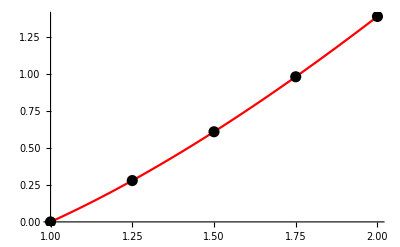

```mathematica
(*въвеждаме условието на задачата*)
a = 1.; b = 2;
x = a;
y = 0.;
points = {{x,y}};
f[x_,y_]:=y/x+1
(*точно решение*)
yt[x_]:=x Log[x]
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " k3= ",k3," k4= ",k4, "y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2*k2+2*k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

## Задача подобна на б) от домашната

търсим точно частно решение:

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x] - Log[x^2+1] + (2x)/(x^2+1)+4, y[2] == 11}, y[x],x]
```

{{y[x]→(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2}}

### РК32 - Формула (1,1)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 3.54764 k2 = 4.37195 y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.25 y_i = 14.9598 f_i = 17.8999 k1 = 4.47498 k2 = 5.53586 y_точно = 14.9959 истинска грешка = 0.0361508

i = 2 x_i = 2.5 y_i = 19.9652 f_i = 22.6739 k1 = 5.66847 k2 = 7.03216 y_точно = 20.0583 истинска грешка = 0.093091

i = 3 x_i = 2.75 y_i = 26.3155 f_i = 28.8105 k1 = 7.20262 k2 = 8.95389 y_точно = 26.4952 истинска грешка = 0.179686

i = 4 x_i = 3. y_i = 34.3938 f_i = 36.6912 k1 = 9.1728 k2 = 11.4202 y_точно = 34.7019 истинска грешка = 0.308126

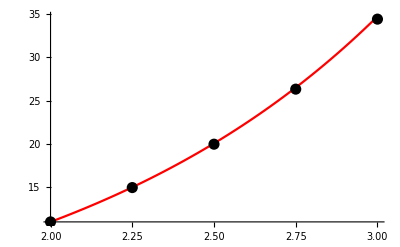

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h,y+k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/2(k1+k2);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

### РК32 - Формула (1/2,1/2) - модифициран метод на Ойлер

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 3.54764 k2 = 3.95919 y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.25 y_i = 14.9592 f_i = 17.8993 k1 = 4.47483 k2 = 5.00467 y_точно = 14.9959 истинска грешка = 0.0367509

i = 2 x_i = 2.5 y_i = 19.9639 f_i = 22.6725 k1 = 5.66813 k2 = 6.3494 y_точно = 20.0583 истинска грешка = 0.0944379

i = 3 x_i = 2.75 y_i = 26.3133 f_i = 28.8082 k1 = 7.20205 k2 = 8.07714 y_точно = 26.4952 истинска грешка = 0.181943

i = 4 x_i = 3. y_i = 34.3904 f_i = 36.6878 k1 = 9.17196 k2 = 10.2951 y_точно = 34.7019 истинска грешка = 0.311498

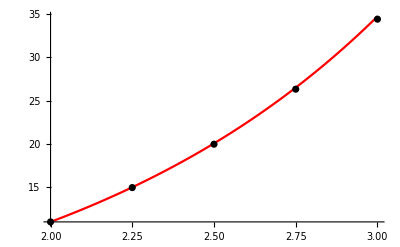

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+h/2,y+k1/2];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК32 - Формула (2/3,2/3)

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.015625

Теоретичната глобална грешка е 0.0625

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 3.54764 k2 = 4.09664 y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.25 y_i = 14.9594 f_i = 17.8995 k1 = 4.47488 k2 = 5.18161 y_точно = 14.9959 истинска грешка = 0.0365508

i = 2 x_i = 2.5 y_i = 19.9643 f_i = 22.673 k1 = 5.66824 k2 = 6.57686 y_точно = 20.0583 истинска грешка = 0.0939874

i = 3 x_i = 2.75 y_i = 26.314 f_i = 28.809 k1 = 7.20224 k2 = 8.36927 y_точно = 26.4952 истинска грешка = 0.181187

i = 4 x_i = 3. y_i = 34.3915 f_i = 36.689 k1 = 9.17224 k2 = 10.6701 y_точно = 34.7019 истинска грешка = 0.310367

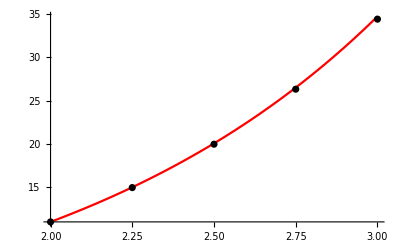

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+2/3*h,y+2/3*k1];

Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+ 1/4 k1 + 3/4 k2;
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки

Мрежата е с n = 4 и стъпка h = 0.25

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.00390625

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 3.54764 k2 = 3.95919 k3= 4.01064 k4= 4.4877y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.25 y_i = 14.9958 f_i = 17.936 k1 = 4.48399 k2 = 5.01498 k3= 5.08135 k4= 5.69646y_точно = 14.9959 истинска грешка = 0.000111306

i = 2 x_i = 2.5 y_i = 20.058 f_i = 22.7667 k1 = 5.69167 k2 = 6.37588 k3= 6.46141 k4= 7.25359y_точно = 20.0583 истинска грешка = 0.000286465

i = 3 x_i = 2.75 y_i = 26.4947 f_i = 28.9896 k1 = 7.2474 k2 = 8.12816 k3= 8.23825 k4= 9.25758y_точно = 26.4952 истинска грешка = 0.00055296

i = 4 x_i = 3. y_i = 34.701 f_i = 36.9984 k1 = 9.24959 k2 = 10.3825 k3= 10.5241 k4= 11.8349y_точно = 34.7019 истинска грешка = 0.000948573

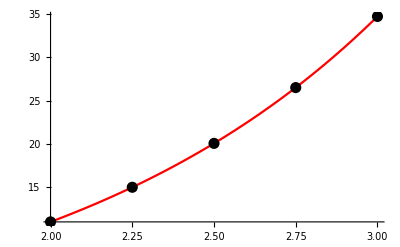

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 4; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " k3= ",k3," k4= ",k4, "y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2*k2+2*k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки - при дадена стъпка h = 0.2

Мрежата е с n = 5. и стъпка h = 0.2

Теоретичната локална  грешка е 0.00032

Теоретичната глобална грешка е 0.0016

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 2.83811 k2 = 3.10143 k3= 3.12776 k4= 3.42329y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.2 y_i = 14.12 f_i = 17.1087 k1 = 3.42173 k2 = 3.74464 k3= 3.77693 k4= 4.13919y_точно = 14.12 истинска грешка = 0.0000361629

i = 2 x_i = 2.4 y_i = 17.8873 f_i = 20.6863 k1 = 4.13727 k2 = 4.53292 k3= 4.57248 k4= 5.01618y_точно = 17.8874 истинска грешка = 0.0000884853

i = 3 x_i = 2.6 y_i = 22.448 f_i = 25.0691 k1 = 5.01383 k2 = 5.49825 k3= 5.5467 k4= 6.08978y_точно = 22.4482 истинска грешка = 0.000162401

i = 4 x_i = 2.8 y_i = 27.9803 f_i = 30.4345 k1 = 6.08689 k2 = 6.67966 k3= 6.73894 k4= 7.40332y_точно = 27.9805 истинска грешка = 0.000264925

i = 5 x_i = 3. y_i = 34.7015 f_i = 36.9989 k1 = 7.39978 k2 = 8.12479 k3= 8.19729 k4= 9.00974y_точно = 34.7019 истинска грешка = 0.0004051

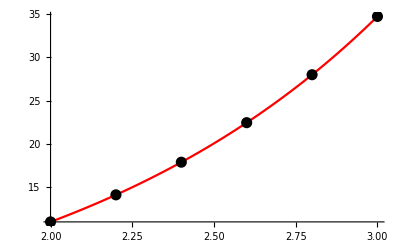

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
h = 0.2;
n =  (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " k3= ",k3," k4= ",k4, "y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2*k2+2*k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки - при дадена стъпка h = 0.01

Мрежата е с n = 100. и стъпка h = 0.01

Теоретичната локална  грешка е 1.×10^-10

Теоретичната глобална грешка е 1.×10^-8

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 0.141906 k2 = 0.142563 k3= 0.142566 k4= 0.143227y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.01 y_i = 11.1426 f_i = 14.3227 k1 = 0.143227 k2 = 0.143892 k3= 0.143895 k4= 0.144563y_точно = 11.1426 истинска грешка = 1.09477×10^-11

i = 2 x_i = 2.02 y_i = 11.2865 f_i = 14.4563 k1 = 0.144563 k2 = 0.145234 k3= 0.145237 k4= 0.145912y_точно = 11.2865 истинска грешка = 2.21103×10^-11

i = 3 x_i = 2.03 y_i = 11.4317 f_i = 14.5912 k1 = 0.145912 k2 = 0.14659 k3= 0.146593 k4= 0.147275y_точно = 11.4317 истинска грешка = 3.35021×10^-11

i = 4 x_i = 2.04 y_i = 11.5783 f_i = 14.7275 k1 = 0.147275 k2 = 0.14796 k3= 0.147963 k4= 0.148652y_точно = 11.5783 истинска грешка = 4.5123×10^-11

i = 5 x_i = 2.05 y_i = 11.7263 f_i = 14.8652 k1 = 0.148652 k2 = 0.149344 k3= 0.149347 k4= 0.150043y_точно = 11.7263 истинска грешка = 5.69695×10^-11

i = 6 x_i = 2.06 y_i = 11.8756 f_i = 15.0043 k1 = 0.150043 k2 = 0.150742 k3= 0.150746 k4= 0.151449y_точно = 11.8756 истинска грешка = 6.90559×10^-11

i = 7 x_i = 2.07 y_i = 12.0263 f_i = 15.1449 k1 = 0.151449 k2 = 0.152155 k3= 0.152158 k4= 0.152868y_точно = 12.0263 истинска грешка = 8.13785×10^-11

i = 8 x_i = 2.08 y_i = 12.1785 f_i = 15.2868 k1 = 0.152868 k2 = 0.153582 k3= 0.153586 k4= 0.154303y_точно = 12.1785 истинска грешка = 9.39426×10^-11

i = 9 x_i = 2.09 y_i = 12.3321 f_i = 15.4303 k1 = 0.154303 k2 = 0.155024 k3= 0.155027 k4= 0.155752y_точно = 12.3321 истинска грешка = 1.06754×10^-10

i = 10 x_i = 2.1 y_i = 12.4871 f_i = 15.5752 k1 = 0.155752 k2 = 0.15648 k3= 0.156484 k4= 0.157216y_точно = 12.4871 истинска грешка = 1.19817×10^-10

i = 11 x_i = 2.11 y_i = 12.6436 f_i = 15.7216 k1 = 0.157216 k2 = 0.157952 k3= 0.157956 k4= 0.158695y_точно = 12.6436 истинска грешка = 1.33129×10^-10

i = 12 x_i = 2.12 y_i = 12.8015 f_i = 15.8695 k1 = 0.158695 k2 = 0.159438 k3= 0.159442 k4= 0.160189y_точно = 12.8015 истинска грешка = 1.467×10^-10

i = 13 x_i = 2.13 y_i = 12.961 f_i = 16.0189 k1 = 0.160189 k2 = 0.16094 k3= 0.160944 k4= 0.161699y_точно = 12.961 истинска грешка = 1.60531×10^-10

i = 14 x_i = 2.14 y_i = 13.1219 f_i = 16.1699 k1 = 0.161699 k2 = 0.162458 k3= 0.162461 k4= 0.163224y_точно = 13.1219 истинска грешка = 1.74632×10^-10

i = 15 x_i = 2.15 y_i = 13.2844 f_i = 16.3224 k1 = 0.163224 k2 = 0.16399 k3= 0.163994 k4= 0.164765y_точно = 13.2844 истинска грешка = 1.88995×10^-10

i = 16 x_i = 2.16 y_i = 13.4484 f_i = 16.4765 k1 = 0.164765 k2 = 0.165539 k3= 0.165543 k4= 0.166321y_точно = 13.4484 истинска грешка = 2.03634×10^-10

i = 17 x_i = 2.17 y_i = 13.6139 f_i = 16.6321 k1 = 0.166321 k2 = 0.167103 k3= 0.167107 k4= 0.167894y_точно = 13.6139 истинска грешка = 2.18554×10^-10

i = 18 x_i = 2.18 y_i = 13.781 f_i = 16.7894 k1 = 0.167894 k2 = 0.168684 k3= 0.168688 k4= 0.169482y_точно = 13.781 истинска грешка = 2.33745×10^-10

i = 19 x_i = 2.19 y_i = 13.9497 f_i = 16.9482 k1 = 0.169482 k2 = 0.17028 k3= 0.170284 k4= 0.171087y_точно = 13.9497 истинска грешка = 2.49235×10^-10

i = 20 x_i = 2.2 y_i = 14.12 f_i = 17.1087 k1 = 0.171087 k2 = 0.171893 k3= 0.171898 k4= 0.172708y_точно = 14.12 истинска грешка = 2.65008×10^-10

i = 21 x_i = 2.21 y_i = 14.2919 f_i = 17.2708 k1 = 0.172708 k2 = 0.173523 k3= 0.173527 k4= 0.174346y_точно = 14.2919 истинска грешка = 2.8108×10^-10

i = 22 x_i = 2.22 y_i = 14.4654 f_i = 17.4346 k1 = 0.174346 k2 = 0.175169 k3= 0.175173 k4= 0.176001y_точно = 14.4654 истинска грешка = 2.97442×10^-10

i = 23 x_i = 2.23 y_i = 14.6406 f_i = 17.6001 k1 = 0.176001 k2 = 0.176832 k3= 0.176836 k4= 0.177672y_точно = 14.6406 истинска грешка = 3.14111×10^-10

i = 24 x_i = 2.24 y_i = 14.8174 f_i = 17.7672 k1 = 0.177672 k2 = 0.178512 k3= 0.178517 k4= 0.179361y_точно = 14.8174 истинска грешка = 3.31093×10^-10

i = 25 x_i = 2.25 y_i = 14.9959 f_i = 17.9361 k1 = 0.179361 k2 = 0.18021 k3= 0.180214 k4= 0.181067y_точно = 14.9959 истинска грешка = 3.48377×10^-10

i = 26 x_i = 2.26 y_i = 15.1762 f_i = 18.1067 k1 = 0.181067 k2 = 0.181924 k3= 0.181928 k4= 0.18279y_точно = 15.1762 истинска грешка = 3.65983×10^-10

i = 27 x_i = 2.27 y_i = 15.3581 f_i = 18.279 k1 = 0.18279 k2 = 0.183656 k3= 0.183661 k4= 0.184531y_точно = 15.3581 истинска грешка = 3.83912×10^-10

i = 28 x_i = 2.28 y_i = 15.5417 f_i = 18.4531 k1 = 0.184531 k2 = 0.185406 k3= 0.185411 k4= 0.18629y_точно = 15.5417 истинска грешка = 4.02165×10^-10

i = 29 x_i = 2.29 y_i = 15.7272 f_i = 18.629 k1 = 0.18629 k2 = 0.187174 k3= 0.187178 k4= 0.188067y_точно = 15.7272 истинска грешка = 4.20744×10^-10

i = 30 x_i = 2.3 y_i = 15.9143 f_i = 18.8067 k1 = 0.188067 k2 = 0.18896 k3= 0.188964 k4= 0.189862y_точно = 15.9143 истинска грешка = 4.39661×10^-10

i = 31 x_i = 2.31 y_i = 16.1033 f_i = 18.9862 k1 = 0.189862 k2 = 0.190764 k3= 0.190768 k4= 0.191675y_точно = 16.1033 истинска грешка = 4.58922×10^-10

i = 32 x_i = 2.32 y_i = 16.2941 f_i = 19.1675 k1 = 0.191675 k2 = 0.192586 k3= 0.192591 k4= 0.193507y_точно = 16.2941 истинска грешка = 4.78526×10^-10

i = 33 x_i = 2.33 y_i = 16.4866 f_i = 19.3507 k1 = 0.193507 k2 = 0.194428 k3= 0.194432 k4= 0.195358y_точно = 16.4866 истинска грешка = 4.98481×10^-10

i = 34 x_i = 2.34 y_i = 16.6811 f_i = 19.5358 k1 = 0.195358 k2 = 0.196288 k3= 0.196292 k4= 0.197227y_точно = 16.6811 истинска грешка = 5.18789×10^-10

i = 35 x_i = 2.35 y_i = 16.8774 f_i = 19.7227 k1 = 0.197227 k2 = 0.198166 k3= 0.198171 k4= 0.199115y_точно = 16.8774 истинска грешка = 5.39458×10^-10

i = 36 x_i = 2.36 y_i = 17.0755 f_i = 19.9115 k1 = 0.199115 k2 = 0.200065 k3= 0.200069 k4= 0.201023y_точно = 17.0755 истинска грешка = 5.60501×10^-10

i = 37 x_i = 2.37 y_i = 17.2756 f_i = 20.1023 k1 = 0.201023 k2 = 0.201982 k3= 0.201987 k4= 0.202951y_точно = 17.2756 истинска грешка = 5.81903×10^-10

i = 38 x_i = 2.38 y_i = 17.4776 f_i = 20.2951 k1 = 0.202951 k2 = 0.203919 k3= 0.203924 k4= 0.204898y_точно = 17.4776 истинска грешка = 6.03684×10^-10

i = 39 x_i = 2.39 y_i = 17.6815 f_i = 20.4897 k1 = 0.204897 k2 = 0.205876 k3= 0.205881 k4= 0.206864y_точно = 17.6815 истинска грешка = 6.25853×10^-10

i = 40 x_i = 2.4 y_i = 17.8874 f_i = 20.6864 k1 = 0.206864 k2 = 0.207853 k3= 0.207858 k4= 0.208851y_точно = 17.8874 истинска грешка = 6.48402×10^-10

i = 41 x_i = 2.41 y_i = 18.0953 f_i = 20.8851 k1 = 0.208851 k2 = 0.20985 k3= 0.209855 k4= 0.210858y_точно = 18.0953 истинска грешка = 6.71349×10^-10

i = 42 x_i = 2.42 y_i = 18.3051 f_i = 21.0858 k1 = 0.210858 k2 = 0.211867 k3= 0.211872 k4= 0.212886y_точно = 18.3051 истинска грешка = 6.94694×10^-10

i = 43 x_i = 2.43 y_i = 18.517 f_i = 21.2886 k1 = 0.212886 k2 = 0.213905 k3= 0.21391 k4= 0.214934y_точно = 18.517 истинска грешка = 7.1844×10^-10

i = 44 x_i = 2.44 y_i = 18.7309 f_i = 21.4934 k1 = 0.214934 k2 = 0.215964 k3= 0.215969 k4= 0.217003y_точно = 18.7309 истинска грешка = 7.42602×10^-10

i = 45 x_i = 2.45 y_i = 18.9468 f_i = 21.7003 k1 = 0.217003 k2 = 0.218043 k3= 0.218048 k4= 0.219094y_точно = 18.9468 истинска грешка = 7.6718×10^-10

i = 46 x_i = 2.46 y_i = 19.1649 f_i = 21.9094 k1 = 0.219094 k2 = 0.220144 k3= 0.220149 k4= 0.221205y_точно = 19.1649 истинска грешка = 7.92173×10^-10

i = 47 x_i = 2.47 y_i = 19.385 f_i = 22.1205 k1 = 0.221205 k2 = 0.222266 k3= 0.222272 k4= 0.223338y_точно = 19.385 истинска грешка = 8.17593×10^-10

i = 48 x_i = 2.48 y_i = 19.6073 f_i = 22.3338 k1 = 0.223338 k2 = 0.22441 k3= 0.224415 k4= 0.225493y_точно = 19.6073 истинска грешка = 8.43453×10^-10

i = 49 x_i = 2.49 y_i = 19.8317 f_i = 22.5493 k1 = 0.225493 k2 = 0.226576 k3= 0.226581 k4= 0.22767y_точно = 19.8317 истинска грешка = 8.69754×10^-10

i = 50 x_i = 2.5 y_i = 20.0583 f_i = 22.767 k1 = 0.22767 k2 = 0.228764 k3= 0.228769 k4= 0.229868y_точно = 20.0583 истинска грешка = 8.96495×10^-10

i = 51 x_i = 2.51 y_i = 20.2871 f_i = 22.9868 k1 = 0.229868 k2 = 0.230974 k3= 0.230979 k4= 0.23209y_точно = 20.2871 истинска грешка = 9.23695×10^-10

i = 52 x_i = 2.52 y_i = 20.5181 f_i = 23.209 k1 = 0.23209 k2 = 0.233206 k3= 0.233212 k4= 0.234334y_точно = 20.5181 истинска грешка = 9.51356×10^-10

i = 53 x_i = 2.53 y_i = 20.7513 f_i = 23.4334 k1 = 0.234334 k2 = 0.235461 k3= 0.235467 k4= 0.2366y_точно = 20.7513 истинска грешка = 9.79476×10^-10

i = 54 x_i = 2.54 y_i = 20.9867 f_i = 23.66 k1 = 0.2366 k2 = 0.237739 k3= 0.237745 k4= 0.23889y_точно = 20.9867 истинска грешка = 1.00807×10^-9

i = 55 x_i = 2.55 y_i = 21.2245 f_i = 23.889 k1 = 0.23889 k2 = 0.240041 k3= 0.240047 k4= 0.241203y_точно = 21.2245 истинска грешка = 1.03714×10^-9

i = 56 x_i = 2.56 y_i = 21.4645 f_i = 24.1203 k1 = 0.241203 k2 = 0.242366 k3= 0.242371 k4= 0.24354y_точно = 21.4645 истинска грешка = 1.06671×10^-9

i = 57 x_i = 2.57 y_i = 21.7069 f_i = 24.354 k1 = 0.24354 k2 = 0.244714 k3= 0.24472 k4= 0.2459y_точно = 21.7069 истинска грешка = 1.09675×10^-9

i = 58 x_i = 2.58 y_i = 21.9516 f_i = 24.59 k1 = 0.2459 k2 = 0.247086 k3= 0.247092 k4= 0.248284y_точно = 21.9516 истинска грешка = 1.1273×10^-9

i = 59 x_i = 2.59 y_i = 22.1987 f_i = 24.8284 k1 = 0.248284 k2 = 0.249483 k3= 0.249489 k4= 0.250693y_точно = 22.1987 истинска грешка = 1.15836×10^-9

i = 60 x_i = 2.6 y_i = 22.4482 f_i = 25.0693 k1 = 0.250693 k2 = 0.251903 k3= 0.251909 k4= 0.253126y_точно = 22.4482 истинска грешка = 1.18993×10^-9

i = 61 x_i = 2.61 y_i = 22.7001 f_i = 25.3126 k1 = 0.253126 k2 = 0.254349 k3= 0.254355 k4= 0.255584y_точно = 22.7001 истинска грешка = 1.22202×10^-9

i = 62 x_i = 2.62 y_i = 22.9544 f_i = 25.5584 k1 = 0.255584 k2 = 0.256819 k3= 0.256825 k4= 0.258067y_точно = 22.9544 истинска грешка = 1.25464×10^-9

i = 63 x_i = 2.63 y_i = 23.2113 f_i = 25.8067 k1 = 0.258067 k2 = 0.259314 k3= 0.259321 k4= 0.260575y_точно = 23.2113 истинска грешка = 1.2878×10^-9

i = 64 x_i = 2.64 y_i = 23.4706 f_i = 26.0575 k1 = 0.260575 k2 = 0.261835 k3= 0.261841 k4= 0.263108y_точно = 23.4706 истинска грешка = 1.32149×10^-9

i = 65 x_i = 2.65 y_i = 23.7324 f_i = 26.3108 k1 = 0.263108 k2 = 0.264381 k3= 0.264388 k4= 0.265667y_точно = 23.7324 истинска грешка = 1.35574×10^-9

i = 66 x_i = 2.66 y_i = 23.9968 f_i = 26.5667 k1 = 0.265667 k2 = 0.266953 k3= 0.26696 k4= 0.268253y_точно = 23.9968 истинска грешка = 1.39055×10^-9

i = 67 x_i = 2.67 y_i = 24.2638 f_i = 26.8253 k1 = 0.268253 k2 = 0.269552 k3= 0.269558 k4= 0.270864y_точно = 24.2638 истинска грешка = 1.42592×10^-9

i = 68 x_i = 2.68 y_i = 24.5333 f_i = 27.0864 k1 = 0.270864 k2 = 0.272176 k3= 0.272183 k4= 0.273502y_точно = 24.5333 истинска грешка = 1.46186×10^-9

i = 69 x_i = 2.69 y_i = 24.8055 f_i = 27.3502 k1 = 0.273502 k2 = 0.274828 k3= 0.274834 k4= 0.276167y_точно = 24.8055 истинска грешка = 1.49839×10^-9

i = 70 x_i = 2.7 y_i = 25.0803 f_i = 27.6167 k1 = 0.276167 k2 = 0.277506 k3= 0.277513 k4= 0.278858y_точно = 25.0803 истинска грешка = 1.5355×10^-9

i = 71 x_i = 2.71 y_i = 25.3578 f_i = 27.8858 k1 = 0.278858 k2 = 0.280211 k3= 0.280218 k4= 0.281578y_точно = 25.3578 истинска грешка = 1.57322×10^-9

i = 72 x_i = 2.72 y_i = 25.6381 f_i = 28.1578 k1 = 0.281578 k2 = 0.282944 k3= 0.282951 k4= 0.284324y_точно = 25.6381 истинска грешка = 1.61153×10^-9

i = 73 x_i = 2.73 y_i = 25.921 f_i = 28.4324 k1 = 0.284324 k2 = 0.285705 k3= 0.285712 k4= 0.287099y_точно = 25.921 истинска грешка = 1.65046×10^-9

i = 74 x_i = 2.74 y_i = 26.2067 f_i = 28.7099 k1 = 0.287099 k2 = 0.288493 k3= 0.2885 k4= 0.289902y_точно = 26.2067 истинска грешка = 1.69002×10^-9

i = 75 x_i = 2.75 y_i = 26.4952 f_i = 28.9902 k1 = 0.289902 k2 = 0.29131 k3= 0.291317 k4= 0.292733y_точно = 26.4952 истинска грешка = 1.73021×10^-9

i = 76 x_i = 2.76 y_i = 26.7865 f_i = 29.2733 k1 = 0.292733 k2 = 0.294155 k3= 0.294163 k4= 0.295593y_точно = 26.7865 истинска грешка = 1.77104×10^-9

i = 77 x_i = 2.77 y_i = 27.0807 f_i = 29.5593 k1 = 0.295593 k2 = 0.29703 k3= 0.297037 k4= 0.298481y_точно = 27.0807 истинска грешка = 1.81251×10^-9

i = 78 x_i = 2.78 y_i = 27.3777 f_i = 29.8481 k1 = 0.298481 k2 = 0.299933 k3= 0.29994 k4= 0.3014y_точно = 27.3777 истинска грешка = 1.85465×10^-9

i = 79 x_i = 2.79 y_i = 27.6777 f_i = 30.14 k1 = 0.3014 k2 = 0.302866 k3= 0.302873 k4= 0.304347y_точно = 27.6777 истинска грешка = 1.89745×10^-9

i = 80 x_i = 2.8 y_i = 27.9805 f_i = 30.4347 k1 = 0.304347 k2 = 0.305829 k3= 0.305836 k4= 0.307325y_точно = 27.9805 истинска грешка = 1.94093×10^-9

i = 81 x_i = 2.81 y_i = 28.2864 f_i = 30.7325 k1 = 0.307325 k2 = 0.308821 k3= 0.308829 k4= 0.310333y_точно = 28.2864 истинска грешка = 1.98508×10^-9

i = 82 x_i = 2.82 y_i = 28.5952 f_i = 31.0333 k1 = 0.310333 k2 = 0.311844 k3= 0.311852 k4= 0.313371y_точно = 28.5952 истинска грешка = 2.02995×10^-9

i = 83 x_i = 2.83 y_i = 28.907 f_i = 31.3371 k1 = 0.313371 k2 = 0.314898 k3= 0.314905 k4= 0.31644y_точно = 28.907 истинска грешка = 2.07551×10^-9

i = 84 x_i = 2.84 y_i = 29.2219 f_i = 31.644 k1 = 0.31644 k2 = 0.317982 k3= 0.31799 k4= 0.31954y_точно = 29.2219 истинска грешка = 2.12178×10^-9

i = 85 x_i = 2.85 y_i = 29.5399 f_i = 31.954 k1 = 0.31954 k2 = 0.321098 k3= 0.321106 k4= 0.322672y_точно = 29.5399 истинска грешка = 2.16878×10^-9

i = 86 x_i = 2.86 y_i = 29.861 f_i = 32.2672 k1 = 0.322672 k2 = 0.324245 k3= 0.324253 k4= 0.325835y_точно = 29.861 истинска грешка = 2.21651×10^-9

i = 87 x_i = 2.87 y_i = 30.1853 f_i = 32.5835 k1 = 0.325835 k2 = 0.327425 k3= 0.327433 k4= 0.32903y_точно = 30.1853 истинска грешка = 2.26499×10^-9

i = 88 x_i = 2.88 y_i = 30.5127 f_i = 32.903 k1 = 0.32903 k2 = 0.330636 k3= 0.330644 k4= 0.332258y_точно = 30.5127 истинска грешка = 2.31421×10^-9

i = 89 x_i = 2.89 y_i = 30.8434 f_i = 33.2258 k1 = 0.332258 k2 = 0.33388 k3= 0.333888 k4= 0.335518y_точно = 30.8434 истинска грешка = 2.3642×10^-9

i = 90 x_i = 2.9 y_i = 31.1772 f_i = 33.5518 k1 = 0.335518 k2 = 0.337157 k3= 0.337165 k4= 0.338812y_точно = 31.1772 истинска грешка = 2.41496×10^-9

i = 91 x_i = 2.91 y_i = 31.5144 f_i = 33.8812 k1 = 0.338812 k2 = 0.340467 k3= 0.340475 k4= 0.342138y_точно = 31.5144 истинска грешка = 2.46651×10^-9

i = 92 x_i = 2.92 y_i = 31.8549 f_i = 34.2138 k1 = 0.342138 k2 = 0.34381 k3= 0.343819 k4= 0.345499y_точно = 31.8549 истинска грешка = 2.51886×10^-9

i = 93 x_i = 2.93 y_i = 32.1987 f_i = 34.5499 k1 = 0.345499 k2 = 0.347188 k3= 0.347196 k4= 0.348893y_точно = 32.1987 истинска грешка = 2.57202×10^-9

i = 94 x_i = 2.94 y_i = 32.5459 f_i = 34.8893 k1 = 0.348893 k2 = 0.350599 k3= 0.350608 k4= 0.352322y_точно = 32.5459 истинска грешка = 2.62597×10^-9

i = 95 x_i = 2.95 y_i = 32.8965 f_i = 35.2322 k1 = 0.352322 k2 = 0.354045 k3= 0.354054 k4= 0.355785y_точно = 32.8965 истинска грешка = 2.68077×10^-9

i = 96 x_i = 2.96 y_i = 33.2505 f_i = 35.5785 k1 = 0.355785 k2 = 0.357526 k3= 0.357535 k4= 0.359284y_точно = 33.2505 истинска грешка = 2.73641×10^-9

i = 97 x_i = 2.97 y_i = 33.6081 f_i = 35.9284 k1 = 0.359284 k2 = 0.361042 k3= 0.361051 k4= 0.362818y_точно = 33.6081 истинска грешка = 2.7929×10^-9

i = 98 x_i = 2.98 y_i = 33.9691 f_i = 36.2818 k1 = 0.362818 k2 = 0.364594 k3= 0.364603 k4= 0.366387y_точно = 33.9691 истинска грешка = 2.85024×10^-9

i = 99 x_i = 2.99 y_i = 34.3337 f_i = 36.6387 k1 = 0.366387 k2 = 0.368181 k3= 0.36819 k4= 0.369993y_точно = 34.3337 истинска грешка = 2.90846×10^-9

i = 100 x_i = 3. y_i = 34.7019 f_i = 36.9993 k1 = 0.369993 k2 = 0.371805 k3= 0.371814 k4= 0.373635y_точно = 34.7019 истинска грешка = 2.96757×10^-9

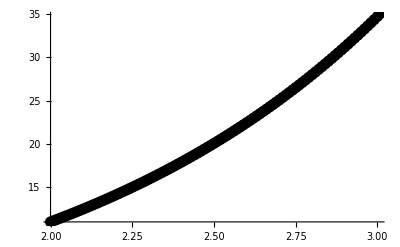

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
h = 0.01;
n =  (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " k3= ",k3," k4= ",k4, "y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2*k2+2*k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки - при зададена точност 10^-7

```mathematica
Clear[n]
Reduce[((b-a)/n)^4<= 10^-7,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-56.2341||n≥56.2341

Мрежата е с n = 57 и стъпка h = 0.0175439

Теоретичната локална  грешка е 1.66198×10^-9

Теоретичната глобална грешка е 9.47328×10^-8

i = 0 x_i = 2. y_i = 11. f_i = 14.1906 k1 = 0.248957 k2 = 0.250981 k3= 0.250999 k4= 0.253041y_точно = 11. истинска грешка = 1.77636×10^-15

i = 1 x_i = 2.01754 y_i = 11.251 f_i = 14.4234 k1 = 0.253041 k2 = 0.255102 k3= 0.25512 k4= 0.2572y_точно = 11.251 истинска грешка = 1.82185×10^-10

i = 2 x_i = 2.03509 y_i = 11.5061 f_i = 14.6604 k1 = 0.257199 k2 = 0.259297 k3= 0.259316 k4= 0.261433y_точно = 11.5061 истинска грешка = 3.70839×10^-10

i = 3 x_i = 2.05263 y_i = 11.7654 f_i = 14.9017 k1 = 0.261433 k2 = 0.263569 k3= 0.263587 k4= 0.265743y_точно = 11.7654 истинска грешка = 5.66153×10^-10

i = 4 x_i = 2.07018 y_i = 12.029 f_i = 15.1473 k1 = 0.265743 k2 = 0.267917 k3= 0.267936 k4= 0.270131y_точно = 12.029 истинска грешка = 7.68306×10^-10

i = 5 x_i = 2.08772 y_i = 12.2969 f_i = 15.3974 k1 = 0.27013 k2 = 0.272344 k3= 0.272364 k4= 0.274598y_точно = 12.2969 истинска грешка = 9.77476×10^-10

i = 6 x_i = 2.10526 y_i = 12.5693 f_i = 15.6521 k1 = 0.274598 k2 = 0.276852 k3= 0.276871 k4= 0.279146y_точно = 12.5693 истинска грешка = 1.19385×10^-9

i = 7 x_i = 2.12281 y_i = 12.8462 f_i = 15.9113 k1 = 0.279146 k2 = 0.28144 k3= 0.28146 k4= 0.283776y_точно = 12.8462 истинска грешка = 1.41764×10^-9

i = 8 x_i = 2.14035 y_i = 13.1276 f_i = 16.1752 k1 = 0.283776 k2 = 0.286112 k3= 0.286132 k4= 0.28849y_точно = 13.1276 истинска грешка = 1.64902×10^-9

i = 9 x_i = 2.15789 y_i = 13.4137 f_i = 16.4439 k1 = 0.288489 k2 = 0.290868 k3= 0.290889 k4= 0.293288y_точно = 13.4137 истинска грешка = 1.8882×10^-9

i = 10 x_i = 2.17544 y_i = 13.7046 f_i = 16.7174 k1 = 0.293288 k2 = 0.295709 k3= 0.295731 k4= 0.298174y_точно = 13.7046 истинска грешка = 2.1354×10^-9

i = 11 x_i = 2.19298 y_i = 14.0003 f_i = 16.9959 k1 = 0.298174 k2 = 0.300639 k3= 0.30066 k4= 0.303147y_точно = 14.0003 истинска грешка = 2.39081×10^-9

i = 12 x_i = 2.21053 y_i = 14.301 f_i = 17.2794 k1 = 0.303147 k2 = 0.305657 k3= 0.305679 k4= 0.308211y_точно = 14.301 истинска грешка = 2.65466×10^-9

i = 13 x_i = 2.22807 y_i = 14.6067 f_i = 17.568 k1 = 0.308211 k2 = 0.310765 k3= 0.310788 k4= 0.313365y_точно = 14.6067 истинска грешка = 2.92717×10^-9

i = 14 x_i = 2.24561 y_i = 14.9174 f_i = 17.8618 k1 = 0.313365 k2 = 0.315966 k3= 0.315989 k4= 0.318613y_точно = 14.9174 истинска грешка = 3.20856×10^-9

i = 15 x_i = 2.26316 y_i = 15.2334 f_i = 18.1609 k1 = 0.318613 k2 = 0.32126 k3= 0.321283 k4= 0.323955y_точно = 15.2334 истинска грешка = 3.49907×10^-9

i = 16 x_i = 2.2807 y_i = 15.5547 f_i = 18.4654 k1 = 0.323955 k2 = 0.32665 k3= 0.326673 k4= 0.329393y_точно = 15.5547 истинска грешка = 3.79893×10^-9

i = 17 x_i = 2.29825 y_i = 15.8814 f_i = 18.7754 k1 = 0.329393 k2 = 0.332136 k3= 0.33216 k4= 0.334929y_точно = 15.8814 истинска грешка = 4.10838×10^-9

i = 18 x_i = 2.31579 y_i = 16.2135 f_i = 19.0909 k1 = 0.334929 k2 = 0.337722 k3= 0.337746 k4= 0.340565y_точно = 16.2135 истинска грешка = 4.42767×10^-9

i = 19 x_i = 2.33333 y_i = 16.5513 f_i = 19.4122 k1 = 0.340564 k2 = 0.343408 k3= 0.343433 k4= 0.346302y_точно = 16.5513 истинска грешка = 4.75705×10^-9

i = 20 x_i = 2.35088 y_i = 16.8947 f_i = 19.7392 k1 = 0.346301 k2 = 0.349196 k3= 0.349221 k4= 0.352142y_точно = 16.8947 истинска грешка = 5.09679×10^-9

i = 21 x_i = 2.36842 y_i = 17.2439 f_i = 20.0721 k1 = 0.352142 k2 = 0.355088 k3= 0.355114 k4= 0.358087y_точно = 17.2439 истинска грешка = 5.44713×10^-9

i = 22 x_i = 2.38596 y_i = 17.599 f_i = 20.411 k1 = 0.358087 k2 = 0.361086 k3= 0.361113 k4= 0.364139y_точно = 17.599 истинска грешка = 5.80837×10^-9

i = 23 x_i = 2.40351 y_i = 17.9601 f_i = 20.7559 k1 = 0.364139 k2 = 0.367192 k3= 0.367219 k4= 0.3703y_точно = 17.9601 истинска грешка = 6.18077×10^-9

i = 24 x_i = 2.42105 y_i = 18.3273 f_i = 21.1071 k1 = 0.3703 k2 = 0.373408 k3= 0.373435 k4= 0.376571y_точно = 18.3273 истинска грешка = 6.56462×10^-9

i = 25 x_i = 2.4386 y_i = 18.7007 f_i = 21.4645 k1 = 0.376571 k2 = 0.379735 k3= 0.379763 k4= 0.382955y_точно = 18.7007 истинска грешка = 6.96019×10^-9

i = 26 x_i = 2.45614 y_i = 19.0805 f_i = 21.8284 k1 = 0.382955 k2 = 0.386176 k3= 0.386204 k4= 0.389454y_точно = 19.0805 истинска грешка = 7.36781×10^-9

i = 27 x_i = 2.47368 y_i = 19.4667 f_i = 22.1988 k1 = 0.389453 k2 = 0.392732 k3= 0.392761 k4= 0.396069y_точно = 19.4667 истинска грешка = 7.78775×10^-9

i = 28 x_i = 2.49123 y_i = 19.8594 f_i = 22.5759 k1 = 0.396068 k2 = 0.399406 k3= 0.399435 k4= 0.402802y_точно = 19.8594 истинска грешка = 8.22034×10^-9

i = 29 x_i = 2.50877 y_i = 20.2589 f_i = 22.9597 k1 = 0.402802 k2 = 0.406199 k3= 0.406229 k4= 0.409657y_точно = 20.2589 истинска грешка = 8.66589×10^-9

i = 30 x_i = 2.52632 y_i = 20.6651 f_i = 23.3504 k1 = 0.409657 k2 = 0.413115 k3= 0.413145 k4= 0.416634y_точно = 20.6651 истинска грешка = 9.12472×10^-9

i = 31 x_i = 2.54386 y_i = 21.0782 f_i = 23.7481 k1 = 0.416634 k2 = 0.420154 k3= 0.420185 k4= 0.423736y_точно = 21.0782 истинска грешка = 9.59716×10^-9

i = 32 x_i = 2.5614 y_i = 21.4984 f_i = 24.153 k1 = 0.423736 k2 = 0.427319 k3= 0.427351 k4= 0.430966y_точно = 21.4984 истинска грешка = 1.00836×10^-8

i = 33 x_i = 2.57895 y_i = 21.9257 f_i = 24.565 k1 = 0.430966 k2 = 0.434613 k3= 0.434645 k4= 0.438325y_точно = 21.9257 истинска грешка = 1.05843×10^-8

i = 34 x_i = 2.59649 y_i = 22.3604 f_i = 24.9845 k1 = 0.438325 k2 = 0.442037 k3= 0.44207 k4= 0.445816y_точно = 22.3604 истинска грешка = 1.10996×10^-8

i = 35 x_i = 2.61404 y_i = 22.8024 f_i = 25.4115 k1 = 0.445815 k2 = 0.449594 k3= 0.449627 k4= 0.45344y_точно = 22.8024 истинска грешка = 1.163×10^-8

i = 36 x_i = 2.63158 y_i = 23.252 f_i = 25.8461 k1 = 0.45344 k2 = 0.457287 k3= 0.45732 k4= 0.461202y_точно = 23.252 истинска грешка = 1.21757×10^-8

i = 37 x_i = 2.64912 y_i = 23.7093 f_i = 26.2885 k1 = 0.461201 k2 = 0.465117 k3= 0.465151 k4= 0.469102y_точно = 23.7093 истинска грешка = 1.27372×10^-8

i = 38 x_i = 2.66667 y_i = 24.1745 f_i = 26.7388 k1 = 0.469102 k2 = 0.473087 k3= 0.473122 k4= 0.477143y_точно = 24.1745 истинска грешка = 1.33149×10^-8

i = 39 x_i = 2.68421 y_i = 24.6476 f_i = 27.1971 k1 = 0.477143 k2 = 0.481199 k3= 0.481235 k4= 0.485328y_точно = 24.6476 истинска грешка = 1.39091×10^-8

i = 40 x_i = 2.70175 y_i = 25.1288 f_i = 27.6637 k1 = 0.485328 k2 = 0.489457 k3= 0.489493 k4= 0.49366y_точно = 25.1288 истинска грешка = 1.45203×10^-8

i = 41 x_i = 2.7193 y_i = 25.6183 f_i = 28.1386 k1 = 0.493659 k2 = 0.497862 k3= 0.497899 k4= 0.50214y_точно = 25.6183 истинска грешка = 1.51488×10^-8

i = 42 x_i = 2.73684 y_i = 26.1162 f_i = 28.622 k1 = 0.50214 k2 = 0.506418 k3= 0.506455 k4= 0.510772y_точно = 26.1162 истинска грешка = 1.57951×10^-8

i = 43 x_i = 2.75439 y_i = 26.6226 f_i = 29.114 k1 = 0.510772 k2 = 0.515126 k3= 0.515164 k4= 0.519558y_точно = 26.6226 истинска грешка = 1.64597×10^-8

i = 44 x_i = 2.77193 y_i = 27.1378 f_i = 29.6148 k1 = 0.519558 k2 = 0.52399 k3= 0.524029 k4= 0.528501y_точно = 27.1378 истинска грешка = 1.71428×10^-8

i = 45 x_i = 2.78947 y_i = 27.6618 f_i = 30.1245 k1 = 0.5285 k2 = 0.533012 k3= 0.533051 k4= 0.537603y_точно = 27.6618 истинска грешка = 1.78452×10^-8

i = 46 x_i = 2.80702 y_i = 28.1948 f_i = 30.6434 k1 = 0.537603 k2 = 0.542195 k3= 0.542235 k4= 0.546868y_точно = 28.1948 истинска грешка = 1.85671×10^-8

i = 47 x_i = 2.82456 y_i = 28.7371 f_i = 31.1715 k1 = 0.546868 k2 = 0.551542 k3= 0.551583 k4= 0.556299y_точно = 28.7371 истинска грешка = 1.9309×10^-8

i = 48 x_i = 2.84211 y_i = 29.2886 f_i = 31.709 k1 = 0.556298 k2 = 0.561056 k3= 0.561097 k4= 0.565897y_точно = 29.2886 истинска грешка = 2.00715×10^-8

i = 49 x_i = 2.85965 y_i = 29.8497 f_i = 32.2561 k1 = 0.565897 k2 = 0.570739 k3= 0.570782 k4= 0.575667y_точно = 29.8497 истинска грешка = 2.0855×10^-8

i = 50 x_i = 2.87719 y_i = 30.4205 f_i = 32.813 k1 = 0.575667 k2 = 0.580595 k3= 0.580639 k4= 0.585611y_точно = 30.4205 истинска грешка = 2.166×10^-8

i = 51 x_i = 2.89474 y_i = 31.0011 f_i = 33.3798 k1 = 0.585611 k2 = 0.590627 k3= 0.590671 k4= 0.595733y_точно = 31.0011 истинска грешка = 2.24871×10^-8

i = 52 x_i = 2.91228 y_i = 31.5918 f_i = 33.9567 k1 = 0.595732 k2 = 0.600838 k3= 0.600883 k4= 0.606035y_точно = 31.5918 истинска грешка = 2.33368×10^-8

i = 53 x_i = 2.92982 y_i = 32.1926 f_i = 34.544 k1 = 0.606034 k2 = 0.611231 k3= 0.611277 k4= 0.61652y_точно = 32.1926 истинска грешка = 2.42095×10^-8

i = 54 x_i = 2.94737 y_i = 32.8039 f_i = 35.1416 k1 = 0.61652 k2 = 0.621809 k3= 0.621856 k4= 0.627193y_точно = 32.8039 истинска грешка = 2.5106×10^-8

i = 55 x_i = 2.96491 y_i = 33.4257 f_i = 35.75 k1 = 0.627192 k2 = 0.632576 k3= 0.632623 k4= 0.638055y_точно = 33.4257 истинска грешка = 2.60266×10^-8

i = 56 x_i = 2.98246 y_i = 34.0583 f_i = 36.3691 k1 = 0.638055 k2 = 0.643534 k3= 0.643582 k4= 0.649111y_точно = 34.0583 истинска грешка = 2.69721×10^-8

i = 57 x_i = 3. y_i = 34.7019 f_i = 36.9993 k1 = 0.649111 k2 = 0.654688 k3= 0.654737 k4= 0.660364y_точно = 34.7019 истинска грешка = 2.7943×10^-8

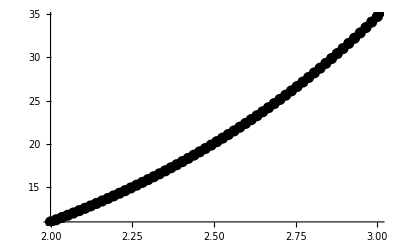

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 57;
h =   (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1 = h*f[x,y];
k2 = h*f[x+1/2 h,y+1/2 k1];
k3 = h*f[x+1/2 h,y+1/2 k2];
k4 = h*f[x+h,y+k3];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " k1 = ", k1 , " k2 = ", k2, " k3= ",k3," k4= ",k4, "y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+1/6(k1+2*k2+2*k3+k4);
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->{Black, PointSize[0.02]}];
Show[gryt,grp]
```

### РК54 - Формула с четири междинни точки - при зададена точност 10^-15 - САМО определяне на мрежата

```mathematica
Clear[n]
Reduce[((b-a)/n)^4<= 10^-15,n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5623.41||n≥5623.41

```mathematica
(*въвеждаме условието на задачата*)
a = 2.; b = 3;
x = a;
y = 11.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1] + (2x)/(x^2+1)+4
(*точно решение*)
yt[x_]:=(-4 ⅇ^2+15 ⅇ^x-ⅇ^x Log[5]+ⅇ^2 Log[1+x^2])/ⅇ^2
(*съставяме мрежата*)
n = 5624;
h =   (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
```

Мрежата е с n = 5624 и стъпка h = 0.000177809

Теоретичната локална  грешка е 1.77735×10^-19

Теоретичната глобална грешка е 9.99583×10^-16